```mathematica
Quit[]
```

# 1. Testing the Short-Duration Gaussian Envelope

```mathematica
(*get your omegas straight*)
```

```mathematica
myWW=1/2;  (*s.t. tc = 2π*)
myTc=Pi/myWW;  (*tc = 2*)
width=2myTc;  (*width of Gaussian*)
(* tg = tgate (gate duration) *)
tg=6width
h1[t_]=Exp[-(t-tg/2)^2/(2*width^2)];
h12[t_]=Exp[-(t-tg*0/2)^2/(2*width^2)];
```

24 π

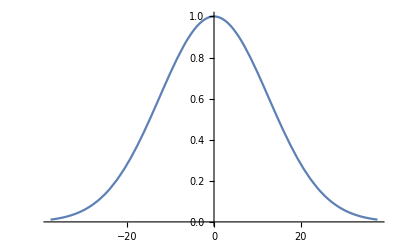

```mathematica
(*Plot[h1[t],{t,0,tg}]*)
Plot[h12[t],{t,-tg/2,tg/2}]
```

```mathematica
Print["This is how many Magnus intervals we appear to need:"]
tg/myTc
```

This is how many Magnus intervals we appear to need:

12

```mathematica
2Pi/width
```

1/2

```mathematica
(*choice:  width=2myTc*)
der[t_,n_]:=D[h12[tt],{tt,n}]/.tt->t;
term[t_,n_]:=der[t,n]/(2myWW)^n;
evalMe=1*tg/4;
term[evalMe,0]//N
term[evalMe,1]//N
term[evalMe,2]//N
term[evalMe,3]//N
term[evalMe,4]//N
term[evalMe,5]//N
term[evalMe,6]//N
term[evalMe,7]//N
```

0.324652

-0.0387525

0.00256986

0.000184052

-0.0000707911

3.78796×10^-6

1.78929×10^-6

-3.57506×10^-7

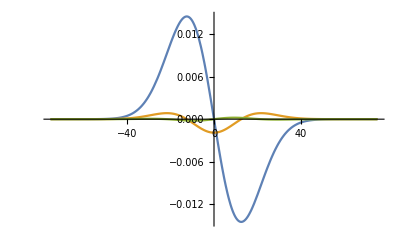

```mathematica
Plot[{.3der[t,1],.3der[t,2],.3der[t,3]},{t,-tg,tg},PlotRange->All]
```

```mathematica
(*
(*choice:  width=myTc*)

der[t_,n_]=D[h1[t],{t,n}];
term[t_,n_]=der[t,n]/(myWW)^n;
evalMe=tg/5;
term[evalMe,1]//N
term[evalMe,2]//N
term[evalMe,3]//N
term[evalMe,4]//N
term[evalMe,5]//N
term[evalMe,6]//N
term[evalMe,7]//N
```

0.113388

0.044915

0.00275726

-0.0120727

-0.00803464

0.00151261

0.00575113

#### Plot H1(t) and its derivatives

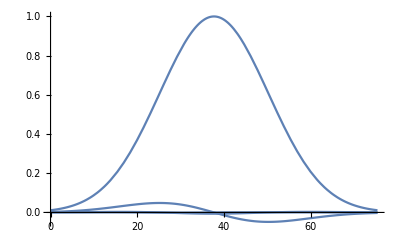

```mathematica
Plot[{h1[t],D[h1[tt],tt],D[h1[tt],{tt,2}],D[h1[tt],{tt,3}]}/.tt->t,{t,0,tg},PlotRange->All]
```

# 2. Compare Hamiltonian Terms

### Write down Hamiltonian Terms

```mathematica
myAAVal=0.02;
replace={myAA->0.02};
```

```mathematica
(* for comparison *)
HRWA=myAA/4×h1[t]/.replace;
Integrate[HRWA/.replace,{t,0,tg/2}]
```

0.0785354

### Write down Hamiltonian Terms

```mathematica
HBS=myAA^2/32
```

Estimate some of the contributions of neglected terms in the time evolution

#### Choose size of amplitude

```mathematica
myAAVal=0.02;
(*myAA=0.001;*)
```

#### Estimate the contribution of H_1^2\16

```mathematica
myAA^2/16
myAA^2/myAA/16
5/64 myAA^3
5/64 myAA^3/myAA
```

6.25×10^-8

0.0000625

7.8125×10^-11

7.8125×10^-8

```mathematica
(*\ddot H1/32*)

(*\dddot H1/32*)
myAA*5*10^-7
(myAA/myAA)*5*10^-7
```

1.×10^-8

5.×10^-7

#### Estimate the contribution of 3H_1\dot H_1/8

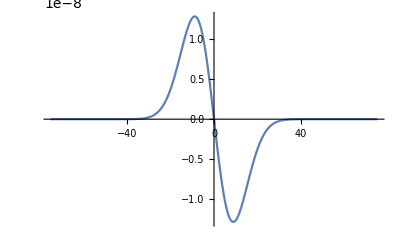

```mathematica
Plot[{3/8 myAA^2 h12[t]der[t,1]},{t,-tg,tg},PlotRange->All]
```

#### Estimate the contribution of (\partial_t)^2 H_1\16

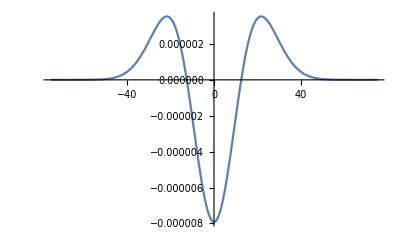

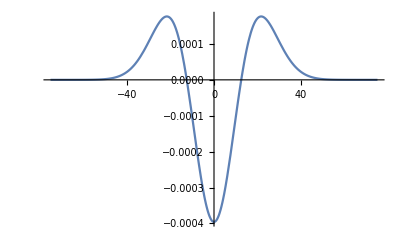

```mathematica
Plot[{1/16 myAA der[t,2]},{t,-tg,tg},PlotRange->All]
(*below:  for the relative estimate*)
Plot[{1/16 myAA/myAA der[t,2]},{t,-tg,tg},PlotRange->All]
```

#### Estimate the contribution of (\partial_t)^3 H_1\16

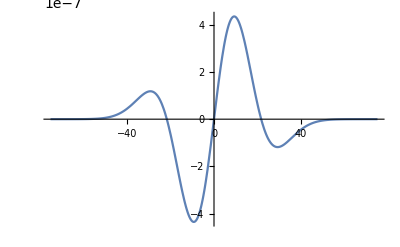

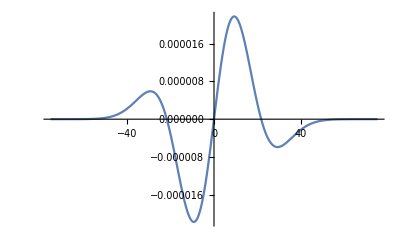

```mathematica
Plot[{1/32 myAA der[t,3]},{t,-tg,tg},PlotRange->All]
(*below:  for the relative estimate*)
Plot[{1/32 myAA/myAA der[t,3]},{t,-tg,tg},PlotRange->All]
```

#### Estimate the contribution of the kick operator

Lowest order (taking into account a jump in the amplitude)

```mathematica
myAA*h12[tg/2]/8
(myAA*h12[tg/2]/8)/myAA
```

1.38862×10^-6

0.00138862

First order (taking into account *only* a jump in the derivative

```mathematica
myAA*der[tg/2,1]/16
(myAA*der[tg/2,1]/16)/myAA
```

-1.65755×10^-7

-0.000165755

Estimate some of the contributions of neglected terms in the time evolution -- via integral

FYI, meaning of standard deviation

### See Gaussian_envelop_simple.nb